```mathematica
eastCombinations=Function[{southSpades,southHearts,eastSpades,eastHearts},Binomial[suit-southSpades,eastSpades]*Binomial[suit-southHearts,eastHearts]*Binomial[suit+southSpades+southHearts,suit-eastSpades-eastHearts]];
```

```mathematica
eastTotalCombinations=Function[{southSpades,southHearts,eastSpades,eastHearts},Plus@@Array[eastCombinations[southSpades,southHearts,eastSpades,#]&,1+suit-eastHearts,eastHearts]];
```

```mathematica
eastSpadesProbability=Function[{southSpades,southHearts,eastSpades,eastHearts},eastTotalCombinations[southSpades,southHearts,eastSpades,eastHearts]/Plus@@Array[eastTotalCombinations[southSpades,southHearts,#,eastHearts]&,1+suit-southSpades,0]//N];
```

```mathematica
arr={0.3,0.5,0.2}
arr[[1]]
a2=
```

{0.3,0.5,0.2}

0.3

0.9

```mathematica
calcMean=Function[probArr,Map[Function[arr,Plus@@Array[#*arr[[#+1]]&,Length[arr],0]],probArr] ];
calcMean[{{1,2,3,4,2,3,4,5,2,4,5,3,2},{1,2,3}}]
```

{261,8}

{{0.504348,4.81942,17.3709,30.5785,28.4651,14.178,3.63573,0.430486,0.017547,0.,0.,0.,0.},{0.588826,5.41031,18.6387,31.2244,27.5852,13.0209,3.16307,0.354908,0.0137207,0.,0.,0.,0.},{0.691916,6.07652,19.935,31.7299,26.6026,11.9137,2.74685,0.292768,0.0107635,0.,0.,0.,0.},{0.815115,6.81246,21.2343,32.0899,25.546,10.869,2.38299,0.241801,0.00847435,0.,0.,0.,0.},{0.959576,7.61114,22.5143,32.3062,24.4414,9.89403,2.06658,0.200049,0.00669809,0.,0.,0.,0.},{1.1261,8.46472,23.7563,32.3855,23.3115,8.99218,1.79251,0.165855,0.00531588,0.,0.,0.,0.},{1.31516,9.3649,24.9454,32.3375,22.1755,8.16367,1.55575,0.137837,0.00423678,0.,0.,0.,0.},{1.52691,10.3033,26.0703,32.1744,21.0487,7.4066,1.35155,0.114852,0.0033913,0.,0.,0.,0.},{1.76122,11.2718,27.1227,31.9091,19.9432,6.7177,1.1756,0.0959672,0.00272634,0.,0.,0.,0.}}

{3.41015,3.33379,3.25732,3.18138,3.10648,3.03299,2.96122,2.89135,2.82353}

{4.29492,4.33311,4.37134,4.40931,4.44676,4.4835,4.51939,4.55432,4.58824}

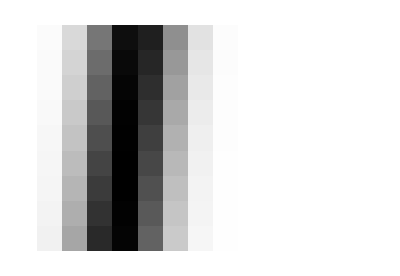

```mathematica
suit=13;
southSpades=1;
eastHearts=5;
eastSpadesprobArr=Array[100*eastSpadesProbability[southSpades,#1,#2,eastHearts]&,{suit+1-Max[southSpades,eastHearts],suit+1-southSpades},{0,0}]
avgEastSpades=calcMean[eastSpadesprobArr]/100
avgNorthSpades=Array[1/2*(suit-southSpades-avgEastSpades[[#]])&,Length[avgEastSpades]]
ArrayPlot[eastSpadesprobArr]
```

```mathematica
(suit-southSpades-avgEastSpades[[1]])/2
```

2.86328

```mathematica
exactCombinations=Function[{mySpades,yourSpades},Binomial[suit-mySpades,yourSpades]*Binomial[2*suit+mySpades,suit-yourSpades]];
```

```mathematica
yourCombinations=Function[{mySpades,yourMinSpades},Plus@@Array[exactCombinations[mySpades,#]&,1+suit-yourMinSpades,yourMinSpades]];
```

```mathematica
yourSpadesProbability=Function[{mySpades,yourMinSpades,yourSpades},If[yourMinSpades≤yourSpades,1,0]*exactCombinations[mySpades,yourSpades] / yourCombinations[mySpades,yourMinSpades]];
```

```mathematica
yourMinSpades=5;
suit=13;
yourSpadesProbArr=Array[yourSpadesProbability[#1,yourMinSpades,#2]&,{1+suit-yourMinSpades,1+suit},{0,0}];
yourAvgSpades=calcMean[yourSpadesProbArr]//N
```

{5.61134,5.49898,5.3996,5.31167,5.23381,5.16477,5.10342,5.04878,5.}

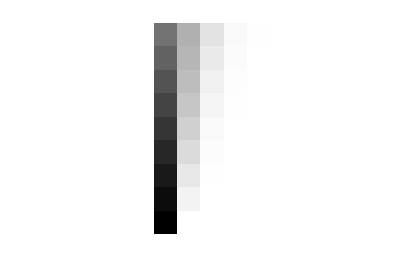

```mathematica
ArrayPlot[probArr]
```